# An Investigation into Global Climate Variables

## ACM40960 - Projects in Mathematical Modelling

## Eilish Clune & Megan Farrell 31st July 2022

## 1. Import Data

We import each of the data-sets that will be used in the analysis. In the following sections we will analyse further:

Temperature Data

Precipitation Data

A case study into Norway and Libya, a high and mid latitude country.

CO_2 data.

We will incorporate knowledge built into Mathematica through the Wolfram Knowledgebase for the study on Norway and Libya, but will import all other data-sets.

The data-sets presented are regularly updated, so we encourage the user to download the data-sets supplied through the GitHub.

### Temperature Data

Three datasets from the Met Office Hadley Centre contain information on monthly temperature anomalies from 1850 to present .  Import all associated datasets, and access their “Attributes” which will load the metadata for each of the datasets. As these are NetCDF files, the datasets contained within each file must be loaded separately to the file.

This first data set contains summary information for the global mean temperature anomalies.

```mathematica
summarytemp = Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.summary_series.global.monthly.nc"];
Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.summary_series.global.monthly.nc", "Attributes"];
```

To import the datasets, iterate over the individual datasets, importing one at a time. The datasets are now stored in the “summaryDatasets” variable.

```mathematica
summaryDatasets =Table[Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.summary_series.global.monthly.nc", {"Datasets", summarytemp[[i]]}], {i, 1, Length[summarytemp]}];
```

The full information regarding the ensemble member mean temperature anomalies dating to 1850 are contained in the Ensemble Members file. Repeat the above process for importing the datasets.

```mathematica
ensembleMembers =Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.ensemble_series.global.monthly.nc"];
Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.ensemble_series.global.monthly.nc", "Attributes"];
```

```mathematica
ensembleDatasets =Table[Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.ensemble_series.global.monthly.nc", {"Datasets", ensembleMembers[[i]]}], {i, 1, Length[ensembleMembers]}];
```

The final data set contains gridded temperature anomalies on a 5^° latitude by 5^° longitude global grid.

```mathematica
tempAnomaly=Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.anomalies.ensemble_mean.nc"];
Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.anomalies.ensemble_mean.nc", "Attributes"];
```

```mathematica
tempAnomalyDatasets =Table[Import[NotebookDirectory[] <> "HadCRUT.5.0.1.0.analysis.anomalies.ensemble_mean.nc", {"Datasets", tempAnomaly[[i]]}], {i, 1, Length[tempAnomaly]}];
```

### Precipitation Data

The precipitation data obtained from the National Oceanic and Atmospheric Administration (NOAA) is loaded below, with its metadata accessed through the “Elements” command.

```mathematica
precipitation = Import[NotebookDirectory[] <> "precip.mon.anom.nc"]
precipInfo =Import[NotebookDirectory[]<> "precip.mon.anom.nc", "Annotations"];
precipDatasets =Table[Import[NotebookDirectory[] <> "precip.mon.anom.nc", {"Datasets", precipitation[[i]]}], {i, 1, Length[precipitation]}];
```

{lat,lon,time,time_bnds,precip}

### CO2 Data

We will work with three data-sets for the CO2 analysis. The data collection is conducted by the NOAA in conjunction with the Global Monitoring Lab (GML). The three files contain information on each of:

Daily global trend in CO_2 in the ten years between 2012 to 2022. This data is obtained from four baseline observatories located in Alaska, Hawaii (Mauna Loa), American Samoa and The South Pole.

Annual CO_2 estimates taken at Mauna Loa observatory in Hawaii from 1959 to 2021.

Monthly CO_2estimates taken at Mauna Loa observatory in Hawaii from March 1958 to June 2022.

More information on these three data-sets is accessed through the metadata, which we will discuss further in Data Cleaning.

```mathematica
globalTrend=Import[NotebookDirectory[]<>"/co2_trend_gl.csv"]; 
annualCO2 = Import[NotebookDirectory[]<>"/co2_annmean_mlo.csv"];
monthlyCO2 = Import[NotebookDirectory[]<>"/co2_mm_mlo.csv"];
```

## 2. Data Cleaning

Here we conduct some preliminary data cleaning and extraction in order to aid our analysis in further sections. This section follows the same order as the data import section.Set up the data so that we can use it to  make plots and produce summary statistics in our investigation of temperature and rain in the context of climate change.

Temperature data-sets.

Precipitation data-sets.

CO_2 data-sets.

Set up the data so that we can use it to  make plots and produce summary statistics in our investigation of temperature and rain in the context of climate change. We also create  a summary function, which we apply to data-set’s throughout the notebook. The summary returns minimum, mean, maximum and lower and upper quartiles of the data.

```mathematica
summary[data_]:=Through[{Min,Quantile[#,0.25]&,Mean,Quantile[#,0.75]&,Max}[data]]
```

### Temperature Datasets

#### Ensemble Members Summary Data

Store the names of the datasets as lists so that we can investigate their properties in more detail . Print the associated datasets in each directory, along with the dimensions:

```mathematica
summaryNames =Table[StringDrop[summarytemp[[i]],{1}],{i,1,Length[summarytemp]}];
Do[Print[summaryNames[[i]], summaryDatasets[[i]]//Dimensions], {i,1,Length[summarytemp]}]
```

realization_bnds{2}

tas_upper{2068}

tas_lower{2068}

time{2068}

longitude{}

latitude{}

bnds{2}

realization{}

latitude_bnds{2}

tas_mean{2068}

time_bnds{2068,2}

longitude_bnds{2}

Combining the information from the file “Attributes” (visible in the Importing Data section), and the dimensions of the results above, we acknowledge that the datasets of interest are the “tas_upper”, “tas_lower” and “tas_mean”. Store these as new datasets, with variable names indicative of what each dataset contains. The Attributes inform us that the datasets “tas_upper” and “tas_lower” contain the 97.5% and 2.5% confidence limits for the ensemble member temperature anomalies,  with the “tas_mean” dataset containing the mean of the temperature anomalies. The dataset containing a list of the times of each observation is also imported, so that we can convert the list of times from their current interval in days since 1850, to represent the years since 1850.

```mathematica
upperlim = summaryDatasets[[2]];
lowerlim = summaryDatasets[[3]];
meanEnsemble = summaryDatasets[[10]];
time = summaryDatasets[[4]];
daystoyears = Table[1850 + UnitConvert[Quantity[time[[i]],"Days"],"Years"][[1]],{i,1,Length[time]}];
```

#### Ensemble Members Dataset

Repeat the process of importing and investigating the properties of the datasets for the full ensemble members file.

```mathematica
ensembleNames=Table[StringDrop[ensembleMembers[[i]],{1}],{i,1,Length[ensembleMembers]}];
Do[Print[ensembleNames[[i]], ensembleDatasets[[i]]//Dimensions], {i,1,Length[ensembleMembers]}]
```

time{2068}

longitude{}

latitude{}

bnds{2}

realization{200}

coverage_unc{2068}

latitude_bnds{2}

area_fraction{2068}

time_bnds{2068,2}

tas{200,2068}

longitude_bnds{2}

Since the first dataset we imported contained summary of the ensemble members dataset, we expect that their time columns contain the same interval between observations.

```mathematica
time == ensembleDatasets[[1]]
```

True

They are the same, so we don’t need to import this information again and we can use the same days-to-years conversion as the summary dataset. 
This dataset contains time-series information on the data of the temperature estimates. The “coverage_unc” and “area_fraction” datasets are both important indicators in the uncertainty in the data for each time period, with “coverage_unc” representing the uncertainty in Kelvin of the statistically infilled temperature estimates, while the “area_fraction” dataset represents the fraction of area that was covered in assembling the ensemble members for that period. The “tas” dataset contains a full record of the 200 ensemble members’ temperature estimates since 1850. The rows are indexed by the ensemble member reference number (1-200), while the columns record the temperature estimate for each time point since 1850.  The reference number for the ensemble members are stored in the “realization” dataset, with this being imported so that looping over the elements of the “tas” dataset is possible.

```mathematica
realisation = ensembleDatasets[[5]];
coverageUncertainty = ensembleDatasets[[6]];
areaFrac = ensembleDatasets[[8]];
tas = ensembleDatasets[[10]];
```

#### Temperature Anomaly Dataset

Extracting the names of the datasets from the file, we then print the dimensions of each dataset in order to investigate their properties.

```mathematica
tempAnomalyNames=Table[StringDrop[tempAnomaly[[i]],{1}],{i,1,Length[tempAnomaly]}];
Do[Print[tempAnomalyNames[[i]], tempAnomalyDatasets[[i]]//Dimensions], {i,1,Length[tempAnomaly]}]
```

realization_bnds{2}

time{2067}

longitude{72}

latitude{36}

bnds{2}

realization{}

latitude_bnds{36,2}

tas_mean{2067,36,72}

time_bnds{2067,2}

longitude_bnds{72,2}

The “Attributes” inform us that the “latitude” data is stored as degrees North, indexed from -90^° to +90^° North, and the “longitude” is indexed from -180^° to +180^° degrees East. The “tas_mean” represents the global gridded temperature data, with a temperature anomaly observation stored for each latitude and longitude pairing. 
We can see that the time dataset has one less observation than the previous ensemble members datasets, so this must also be imported.

```mathematica
timeAnom = tempAnomalyDatasets[[2]];
templon = tempAnomalyDatasets[[3]];
templat = tempAnomalyDatasets[[4]];
tempMeans = tempAnomalyDatasets[[8]];
```

If we tried to access the temperatures at a specific latitude and longitude for all time, we would get errors due to the data containing missing values. The file Metadata, which can be accessed through the file “Attributes” (Importing Data Section), informs us that missing values are stores as  -1 × 10^-30. Set this as a flag value so that missing values can later be removed.

```mathematica
flag = tempMeans[[1,1,1]]
```

-1.×10^30

Create a new table to store values from the time dataset to represent years since 1850 instead of days since 1850, so that plot axes will be more indicative of the time they represent.

```mathematica
temptimeconvert = Table[1850+UnitConvert[Quantity[timeAnom[[i]],"Days"],"Years"][[1]],{i,1,Length[timeAnom]}];
```

### Precipitation Dataset

Extracting the names of the datasets from the file, we then print the dimensions of each of the datasets in order to investigate their properties.

```mathematica
precipNames=Table[precipitation[[i]],{i,1,Length[precipitation]}];
Do[Print[precipitation[[i]], precipDatasets[[i]]//Dimensions], {i,1,Length[precipitation]}]
```

lat{36}

lon{72}

time{1385}

time_bnds{1385,2}

precip{1385,36,72}

The “Annotations” element of the precipitation file contains information on what each dataset contains. The “lat” dataset contains the latitudes, in degrees North of the associated gridded values, with 36 values of latitude stored to represent the grid lines. The latitude data extends from +90^° to -90^° North, which is the opposite direction used for indexing the Temperature Anomaly Data. The “lon” dataset stores 72 longitude values, in degrees East, with the degrees extending from the Prime Meridian , at 0^°East, to +357.5^° East in a full rotation of the Earth, which does not align with the Temperature Anomaly Data indexing, where the longitudes are stored as -180^° to +180^° degrees East . 
The “precip” dataset contains the gridded precipitation anomalies, relative to the 1971 - 2000 reference period. Time is indexed across 1385 observations, with time recorded in days since 1800.
Store the directories as individual data sets so we can access their contents.

```mathematica
precipLat = precipDatasets[[1]];
precipLon = precipDatasets[[2]];
precipTime = precipDatasets[[3]];
precip = precipDatasets[[5]];
```

From the Metadata for this dataset, we know that missing values are stored as -9.96921 × 10^36. Find one such value in the data and store it as a flag value, so that plots will be produced without errors.

```mathematica
precipFlag = precip[[1,1,1]]
```

-9.96921×10^36

Convert the time values from “days since 1800” to represent “years since 1800”:

```mathematica
preciptimeconvert = Table[1800+UnitConvert[Quantity[precipTime[[i]],"Days"],"Years"][[1]], {i, 1, Length[precipTime]}];
```

### CO2 Data

We examine each of the three CO_2 data-sets. The first lines of the csv files contain meta-data, which explains the data set-up along with usage. The data of interest seems to be on line x for each of the dataset.

Global Trend,  x = 61.

Annual CO2, x = 56.

Monthly CO2, x = 52.

We encourage the reader to scroll through the meta-data lines of the three data-sets for further understanding of the CO_2data.

```mathematica
globalTrend//Dataset
annualCO2//Dataset
monthlyCO2//Dataset
```

We will overwrite the data to begin at row x, containing all columns, in order to conduct a clean analysis.

```mathematica
globalTrend = globalTrend[[61;;, ;;]];
annualCO2 = annualCO2[[56;;, ;;]];
monthlyCO2 = monthlyCO2[[52;;, ;;]];
```

#### CO_2 Ticks

Daily global CO_2 estimates 2012 - 2022

Create tick list for the plot.

```mathematica
Range[100, 3750, 365]
```

{100,465,830,1195,1560,1925,2290,2655,3020,3385,3750}

```mathematica
tickListCO1 = {{100, "2012"}, {465, "2013"}, {830, "2014"}, {1195, "2015"}, {1560, "2016"}, {1925, "2017"}, {2290, "2018"}, {2655, "2019"}, {3020, "2020"}, {3385,"2021"}, {3750,"2022"}};
```

Annual global CO_2estimates 1959 - 2021

```mathematica
tickListCO2 = {{10, "1967"}, {20, "1977"}, {30, "1987"}, {40, "1997"}, {50, "2007"}, {60, "2017"}}
```

{{10,1967},{20,1977},{30,1987},{40,1997},{50,2007},{60,2017}}

Monthly global estimates CO_2 March 1958 - June 2022

```mathematica
tickListCO3 = {{205, "1975"}, {385, "1990"}, {565, "2005"}, {745, "2020"}}
```

{{205,1975},{385,1990},{565,2005},{745,2020}}

## 3. Overview Plots

### Temperature Data

#### Summary Ensemble Members

A plot of the summary ensemble members data, showing the mean ensemble member and the 95% confidence limits. The ListPlot command is plotting Tables of data for each of the 2.5% confidence limits, the mean ensemble temperature anomalies, and the 97.5% confidence limit of the ensemble temperature anomalies. Using the “daystoyears” conversion table, we change the plot axes to represent the year of the observations.

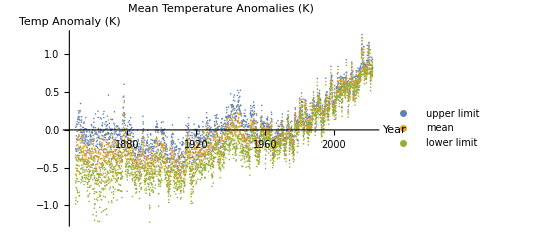

```mathematica
ListPlot[{Table[{daystoyears[[i]],upperlim[[i]]},{i, 1, Length[upperlim]}],Table[{daystoyears[[i]],meanEnsemble[[i]]}, {i, 1, Length[meanEnsemble]}],Table[{daystoyears[[i]],lowerlim[[i]]},{i, 1, Length[lowerlim]}]},AxesLabel -> {"Year", "Temp Anomaly (K)"},TicksStyle->Directive[14],
PlotLabel->"Mean Temperature Anomalies (K)",
PlotLegends->{"upper limit", "mean" ,  "lower limit"}]
```

Print the mean of the ensemble member realisations at the first observation, and for the most recent observation:

```mathematica
meanEnsemble[[1]]
meanEnsemble[[2068]]
```

-0.674564

0.771561

#### The Ensemble Members

Investigate the temperature anomalies of the ensemble members for an observation in the initial period of the record, and the most recent time record. Each ListPlot loops over all ensemble members for the time index chosen in order to plot them, and we place the plots side by side using the GraphicsRow function. The 5^th observation matches in time of year to the most recent observation, so plot these to provide an initial comparison.

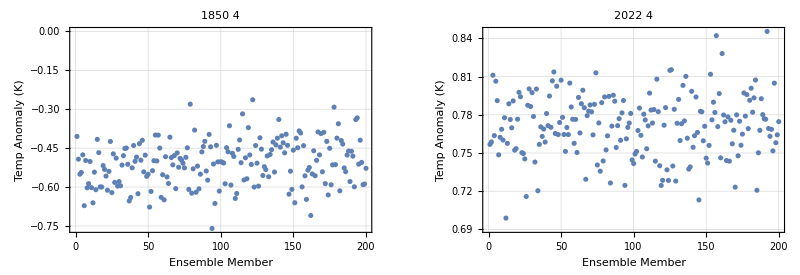

```mathematica
GraphicsRow[{ListPlot[Table[tas[[i, 5]], {i, 1, Length[realisation]}], GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Ensemble Member", ""}},PlotLabel->UnitConvert[Quantity[MixedMagnitude[{1850 , time[[5]] }],MixedUnit[{"Years","Days"}]],MixedUnit[{"Years","Months","Days"}]]], ListPlot[Table[tas[[i, 2068]], {i, 1, Length[realisation]}],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Ensemble Member", ""}},PlotLabel->UnitConvert[Quantity[MixedMagnitude[{1850 , time[[2068]] }],MixedUnit[{"Years","Days"}]],MixedUnit[{"Years","Months","Days"}]]]}]
```

The first plot contains the ensemble member temperatures for the 13^thMay 1850, which are all below the average temperature of the reference period of 1961-1990. The most recent observation is the 25^thMay 2022, with all ensemble members representing times which are above the mean of the ensemble member reference period. I chose these dates in order to compare approximately the temperature of the same time of year. We can investigate the full range of temperatures for the full time record of all ensemble members. The ListPlot loops over all ensemble members i and all time j in order to plot the trend of temperatures in this dataset. Use the converstion table to loop over the same time index j, in order to convert the axis labels to years.

```mathematica
ListPlot[Table[{daystoyears[[j]],tas[[i,j]]}, {i, 1, Length[realisation]}, {j, 1, Length[time]}], PlotLabel->"Ensemble Means", AxesLabel -> {"Year", "Temp Anomaly (K)"}, TicksStyle->Directive[14]]
```

-Graphics-

Each dot represents an ensemble member temperature estimate for the time point represented across the x-axis. For each point in time there are 200 ensemble members. The range of the temperatures across the early period of the record can be explained by the uncertainty in the historical data and the measurement techniques used. This can be investigated by plotting the “coverage_unc” and “area_fraction” datasets. Loop over these datasets for the range of observations to plot the uncertainty estimates, converting the x-axis to years.

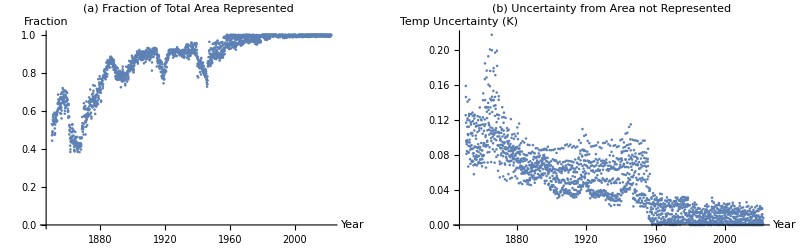

```mathematica
GraphicsRow[{ListPlot[Table[{daystoyears[[i]],areaFrac[[i]]}, {i, 1, Length[areaFrac]}], AxesLabel -> {"Year", "Fraction"},PlotLabel->Style["(a) Fraction of Total Area Represented",13]], ListPlot[Table[{daystoyears[[i]],coverageUncertainty[[i]]}, {i, 1, Length[coverageUncertainty]}], AxesLabel -> {"Year", "Temp Uncertainty (K)"},PlotLabel->Style["(b) Uncertainty from Area not Represented", 13]]}]
```

The fraction of area across the globe that is represented by the ensemble members in the early period of the data is much less than what the data represents since approximately the 1990’s. There are also some notable fluctuations throughout history that can been seen to correspond to periods of global unrest (mentioned in Morice (2020)). As the fraction of area coverage has increased, the temperature uncertainty in the ensemble members has decreased, with less than a 0.05 K uncertainty estimate in the ensemble member temperatures since the 1960’s. This correlates to the previous plot, as we see the ensemble member temperature estimates having less spread in recent years than in the initial period of the study.

#### Temperature Anomaly Plots

Plot the temperature anomalies as a function of longitude, for the most recent time value at the South Pole, which is stored as the first latitude value .

```mathematica
templat[[1]]
```

-87.5

For each of the entries across the “templon” data, plot the associated temperature across the first latitude band in the data. The x-axis is converted to represent the longitude of each of the plotted points. The plot label indicates the year in which we have chosen to investigate the temperature for.

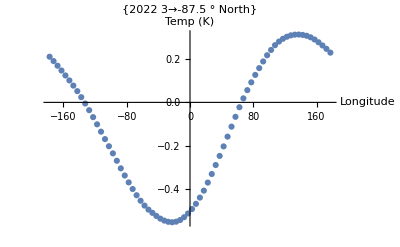

```mathematica
ListPlot[Table[{templon[[i]],tempMeans[[2067, 1, i]]}, {i,1,Length[templon]}], AxesLabel->{"Longitude", "Temp (K)"}, PlotLabel->{UnitConvert[Quantity[MixedMagnitude[{1850 , timeAnom[[2067]] }],MixedUnit[{"Years","Days"}]],MixedUnit[{"Years","Months","Days"}]]->templat[[1]] "° North"}]
```

As we can see, the data represents day and night fluctuations across the longitude, with temperatures dipping for the mid-easterly latitudes while the westerly latitudes have peaked during the daylight hours. We can also see that this is in April, which is an autumn month in the southern hemisphere. Investigate the temperatures for the same period in the Arctic, which is stored as the last value in the “templat” dataset. Access this through the index [[-1]], we can compare the temperatures of each location.

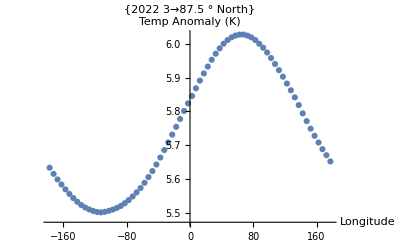

```mathematica
ListPlot[Table[{templon[[i]],tempMeans[[2067, -1, i]]}, {i,1,Length[templon]}], AxesLabel->{"Longitude", "Temp Anomaly (K)"}, PlotLabel->{UnitConvert[Quantity[MixedMagnitude[{1850 , timeAnom[[2067]] }],MixedUnit[{"Years","Days"}]],MixedUnit[{"Years","Months","Days"}]]->templat[[-1]] "° North"}]
```

We can see that the Arctic temperatures are all above the mean temperature anomaly relative to the 1961-1990 climatology period. These plots are hard to compare since we are dealing with the time of year.
Plot the temperatures at these latitudes, choosing a specific longitude to investigate, for all time. In order to plot the available time series data for that  coordinate, iterate over the full data for the specific latitude longitude pairs, removing the flagged missing value value anywhere it appears.
The table representing years since 1850 is also iterated through in order to plot these as the x-axis tick labels.

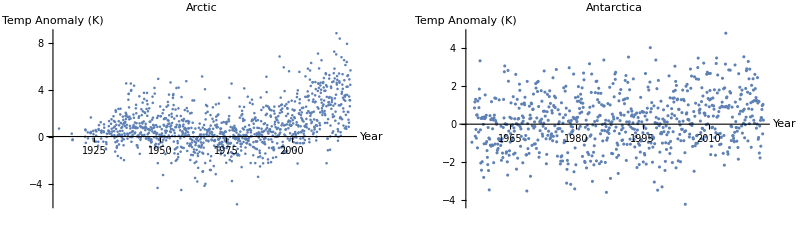

```mathematica
GraphicsRow[{ListPlot[Select[Table[{temptimeconvert[[i]],tempMeans[[i, -1, 1]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &], PlotLabel->"Arctic", AxesLabel->{"Year", "Temp Anomaly (K)"}], ListPlot[Select[Table[{temptimeconvert[[i]],tempMeans[[i, 1, 1]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &], PlotLabel->"Antarctica",AxesLabel->{"Year", "Temp Anomaly (K)"}]}]
```

The temperature increase in the Arctic is much more apparent than the temperature increase in Antarctica, with a steep rise in temperatures since the 1980’s. Due to the missing values being removed, we see data represented in these locations across different time scales, with data only available in Antarctica since approximately 1955.  The increase in temperatures across the Arctic is in line with studies which suggest that the high latitudes are experiencing the most warming due to climate change.

The above conversion which was applied to the axes to convert the Tick Labels from “days since 1850” to “years since 1850” does not work for plots where we are applying a linear fit to the data. This is because the linear fits will be applied to the data based off their indexes, and as a result the equation can not be extended to fit a line overlaid on the temperature data points when the axes would be forced to have different scales. Instead of forcing the plot, we can access the tick labels defined below, which will replace the defaults that the plotting command produces.
Creating tick labels for the plotting axes:

```mathematica
ticks = Table[temptimeconvert[[i]], {i, 800, 2000, 200}];
ticks8002000 = {{800, "1917"}, {1000, "1933"}, {1200, "1950"}, {1400, "1967"}, {1600, "1983"}, {1800,"2000"},{2000, "2017"}};
ticks = Table[temptimeconvert[[i]], {i, 500, 2000, 500}];ticks5002000 = {{500, "1892"}, {1000, "1933"}, {1500, "1975"}, {2000, "2017"}};
ticks = Table[temptimeconvert[[i]], {i, 1000, 2000, 500}];
ticks10002000 = {{1000, "1933"}, {1500, "1975"}, {2000, "2017"}};
```

### Precipitation Plots

Taking inspiration from the initial investigation into the temperature anomaly dataset, plot values for two locations, while removing the flagged value for this dataset. Data is not as extensively available for the Precipitation data, so there was no data for the locations we chose in the previous section. Instead,

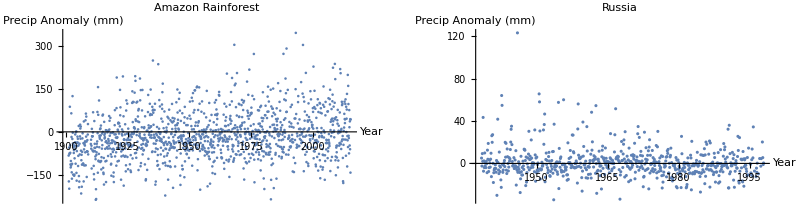

```mathematica
GraphicsRow[{ListPlot[Select[Table[{preciptimeconvert[[i]],precip[[i, 19, 60]]}, {i, 1, Length[precipTime]}], #[[2]]≠precipFlag &], PlotLabel->"Amazon Rainforest", AxesLabel->{"Year", "Precip Anomaly (mm)"}, PlotRange->All], ListPlot[Select[Table[{preciptimeconvert[[i]],precip[[i, 5, 24]]}, {i, 1, Length[precipTime]}], #[[2]]≠precipFlag &], PlotLabel->"Russia", AxesLabel->{"Year", "Precip Anomaly (mm)"}, PlotRange->All]}]
```

Two initial sets of longitude and latitude coordinates show us the distribution of precipitation anomaly patterns for all observations since approximately 1900 in the Amazon Rainforest, and the 1940’s in Russia. We see the Amazon has a larger variation in anomaly events, with some months experiencing 200mm of rainfall less than the average of the reference period, with maxima at approximately 300mm more than the reference period. The anomaly patterns for precipitation in Russia have more concentrated bounds, with a maximum anomaly  of approximately 120mm, while it experienced a minima of approximately -40mm. We can print these maxima and minima anomalies for each loaction:

```mathematica
Print["Amazon Rainforest: [" ,Max[Select[Table[precip[[i, 19, 60]], {i, 1, Length[precipTime]}], #≠precipFlag &]],",",
Min[Select[Table[precip[[i, 19, 60]], {i, 1, Length[precipTime]}], #≠precipFlag &]], "]"]
Print["Russia: [" ,Max[Select[Table[precip[[i, 5, 24]], {i, 1, Length[precipTime]}], #≠precipFlag &]],",",
Min[Select[Table[precip[[i, 5, 24]], {i, 1, Length[precipTime]}], #≠precipFlag &]], "]"]
```

Amazon Rainforest: [344.53,-236.44]

Russia: [123.3,-34.37]

As in the section describing the temperature anomaly data, I will create a list of the tick marks needed to replace the index along the x-axis in order to represent years since 1800. The most recent observation is stored as the 1,385^th entry of the precipitation anomaly data, so we will access this value and convert it to the year it represents, in order for this to be the final tick mark on the plots. All other tick marks are looped through the indexes of the dataframe to replace the default tick marks which Mathematica would use based off the indexes.

```mathematica
1800 + UnitConvert[Quantity[precipTime[[1385]],"Days"],"Years"][[1]];
pticks = Table[preciptimeconvert[[i]], {i, 200, 1200, 200}];
pticks2001400 = {{200, "1917"},{400, "1933"},{600, "1950"},{800, "1967"}, {1000, "1983"}, {1200, "2000"}, {1385, "2015"}};
```

```mathematica
pticks = Table[preciptimeconvert[[i]], {i, 600, 1200, 200}];
pticks6001400 = {{600, "1950"},{800, "1967"}, {1000, "1983"}, {1200, "2000"}, {1385, "2015"}};
```

```mathematica
pticks = Table[preciptimeconvert[[i]], {i, 800, 1200, 200}];
pticks8001400 = {{800, "1967"}, {1000, "1983"}, {1200, "2000"}, {1385, "2015"}};
```

```mathematica
pticks = Table[preciptimeconvert[[i]], {i, 700, 1300, 100}];
pticks7001400 = {{700, "1958"},{800, "1967"},{900, "1975"}, {1000, "1983"}, {1100, "1992"},{1200, "2000"},{1300, "2008"}, {1385, "2015"}};
```

```mathematica
pticks = Table[preciptimeconvert[[i]], {i, 400, 1100, 100}];
pticks4001100 = {{400, "1933"},{500, "1942"},{600, "1950"},{700, "1958"},{800, "1967"},{900, "1975"}, {1000, "1983"}, {1100, "1992"}};
pticks5001100 = {{500, "1942"},{600, "1950"},{700, "1958"},{800, "1967"},{900, "1975"}, {1000, "1983"}, {1100, "1992"}};
```

## 4. Noway & Libya Case Studies

The overall objective of the analysis into Norway and Libya has been guided by a notebook provided in the module “Mathematica for Research” taught by Dr Niels Warburton. The notebook provided titled “Climate Change in the Arctic” presents similar ideology around mapping temperature data in a high-latitude country to represent climate change in the Arctic, and focuses on Greenland.

### Entity Class

To guide our study into different latitude countries, we take a look at the five largest deserts around the world. They are:

Antarctic Polar Desert;

Arctic Polar Desert;

Sahara Subtropical Desert;

Arabian Subtropical Desert;

Gobi Cold Winter Desert.

```mathematica
Entity["Desert"]// EntityList; (* huge number of deserts in the world *)
EntityClass["Desert", "Area"->TakeLargest[5]]// EntityList (* 5 largest deserst *)
```

{Antarctic Desert,Arctic,Sahara,Arabian Desert,Gobi Desert}

Looking at the datasets for each of the five deserts shows the Arctic and the Sahara to border the most land-masses, with each desert bordering 8 and 10 countries, respectively.

#### Arctic Polar Desert

The Arctic is the second largest polar type desert, after the Antarctic Desert. The Arctic has an area of 1.37 x 10^7 km^2 and is located at a point latitude of 85.ba North of the equator. The Arctic borders 8 countries, amongst them is Norway. We will choose Norway due to its proximity to the Arctic, and investigate it under the banner of a high latitude country in order the see temperature and precipitation changes over time in the country.

```mathematica
arctic = Entity["Desert", "Arctic"];
arctic["Dataset"]
```

We can drop a GeoMarker at the exact stated co-ordinates of the Arctic and plot it on a world map.

```mathematica
GraphicsGrid[{{GeoListPlot[GeoMarker[arctic], GeoRange->Quantity[300,"Miles"],  GeoBackground->"StreetMap", PlotLabel->"Arctic Polar Desert"],
GeoListPlot[GeoMarker[arctic], GeoRange->"World",  GeoBackground->"Satellite", PlotLabel->"Arctic Polar Desert - Satellite Image"] }}, ImageSize->Large]
```

-Graphics-

#### Sahara Desert

The Sahara is the third largest desert in the world and the largest sub-tropical type desert, with an area of 9.10 x 10^6 km^2. The Sahara is positioned at point co-ordinates 26.ba North and 13.ba East, although of course stretches across vast latitude-longitude regions. The Sahara borders 10 countries in Africa, amongst them is Libya, which we will investigate it under the banner of a mid latitude country in order the see temperature and precipitation changes over time in the country, and compare against Norway.

```mathematica
sahara= Entity["Desert", "Sahara"];
sahara["Dataset"]
```

From the satellite image of Africa, apparent is the span of the Sahara across North Africa. Missing from the plot is the delineation between the Sahara and the Arabian Subtropical Desert, located east of the Sahara.

```mathematica
GraphicsGrid[{{GeoListPlot[GeoMarker[sahara], GeoRange->"Country", GeoBackground->"StreetMap", PlotLabel->"Sahara Desert"], GeoListPlot[GeoMarker[sahara], GeoRange->Quantity[2000,"Miles"], GeoBackground->"Satellite", PlotLabel->"Sahara Desert - Satellite Image"]}}, ImageSize->Large]
```

-Graphics-

### Norway

We examine Norway in order to inspect the effects of global warming in a high latitude country. The capital city Oslo is located in the south-east of Norway at 59.91.ba North and 10.75.ba East. The country has a population of just under 5.5 million people, with a life expectancy of 82.35 years. The country has a GDP of $3.62522 x 10^11 per year.

```mathematica
norway = CountryData["Norway"]
norway["CapitalCity"]
```

Norway

Oslo

We plot Norway as StreetMap and Satellite images, with Oslo highlighted by a GeoMarker. From the satellite map we can see patches of snow in the country.

```mathematica
GraphicsGrid[{{GeoListPlot[{norway, GeoMarker[norway["CapitalCity"]]},GeoBackground -> "StreetMap", PlotLabel -> "Oslo, Norway"],GeoListPlot[{norway, GeoMarker[norway["CapitalCity"]]},GeoBackground -> "Satellite",PlotLabel -> "Satellite Map - Oslo, Norway"]}}, ImageSize -> 600]
```

-Graphics-

We can extract  co-ordinates of the capital city, along with some socio-economic details.

```mathematica
CityData[{"Oslo", "Oslo", "Norway"}, "Coordinates"]
```

{59.91,10.75}

```mathematica
CountryData["Norway","Population"]
CountryData["Norway","LifeExpectancy"]
CountryData["Norway","GDP"]
CountryData["Norway","GDPRealGrowth"]
```

5421242 people

82.35 yr

3.62522×10^11 $

-0.0076586 $

In the next sections we will look at temperature and precipitation data for Oslo over 60 years between 1960 and 2020.

#### Daily Mean Temperature

We look at the WeatherData entity within Mathematica, focusing on daily mean temperature. Mathematica returns temperature in degrees Celsius (.baC). We apply the summary to the data in order to get the minimum, mean, maximum and lower and upper quartiles. There is clearly a high disparity between 2020 and 1960 in terms of the summary statistics for temperature data in Oslo.

```mathematica
tempData["Oslo",2020]=WeatherData["Oslo","MeanTemperature",{{2020,1},{2020,12},"Day"}];tempData["Oslo",1960]=WeatherData["Oslo","MeanTemperature",{{1960,1},{1960,12},"Day"}];
```

```mathematica
summary[tempData["Oslo", 2020]] 
summary[tempData["Oslo", 1960]]
```

{-4.17 °C,3.44 °C,8.68463 °C,13.61 °C,24.94 °C}

{-18.28 °C,-1.33 °C,4.06443 °C,12.39 °C,21.5 °C}

#### Daily Mean Temperature Oslo - TimeShift

In order to get a full view across both years, 2020 and 1960, we overlay both years on each other by incorporating TimeShift. By doing so we can see that both years follow a similar trend across time-points. However, winter temperatures in Norway are much cooler for the 1960 compared to 2020. This is an important observation given the literature review conducted on the topic, indicating that warming in high latitude countries would be pronounced in winter months due to climate change.

```mathematica
DateListPlot[{tempData["Oslo",2020],TimeSeriesShift[tempData["Oslo",1960],{60,"Year"}]},GridLines->Automatic,PlotLabels->{"2020","1960"},PlotLabel->"Daily Mean Temperature (.baC) Oslo: 1960, 2020"]
```

-Graphics-

#### Linear Fit - Oslo

We create a linear model for the temperature data in Oslo between the years 1960 to 2020. Before creating the model, we inspect missing data entries, which we choose to drop from the data-set. Missing data for Norway for certain years seems to be a problem, https://weatherspark.com/h/y/68697/1970/Historical-Weather-during-1970-in-Oslo-Norway.

```mathematica
Monitor[Do[tempData["Oslo",year]=WeatherData["Oslo","MeanTemperature",{{year,1},{year,12},"Day"}],{year,1960,2020}],year];
```

```mathematica
resNor=Table[tempData["Oslo",year],{year,1960,2020}];
```

Examine missing data-points.

```mathematica
Flatten@Position[resNor,Missing["NotAvailable"]]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
filteredNor = DeleteCases[resNor, _Missing];
```

```mathematica
resNor2=Map[{#["FirstDate"]["Year"],Mean[#]}&,filteredNor];
```

We create the linear fit for Norway and overlay the linear model on the temperature data across the years from 1960 to 2020.

-191.18 °C+x (0.0986004 °C)

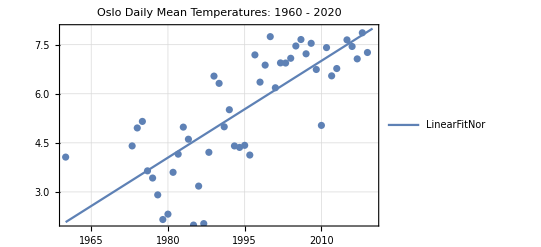

```mathematica
LinearFitNor=Fit[resNor2,{1,x},x]
Show[
Plot[LinearFitNor,{x,1960,2020},PlotTheme->"Detailed"],
ListPlot[resNor2], PlotLabel->"Oslo Daily Mean Temperatures: 1960 - 2020"]
```

#### Oslo - Total monthly precipitation

We look next at total monthly precipitation in Oslo, Norway and we implement analysis very similar to the temperature data. Total precipitation is measured in centimetres (cm). It was not possible to retrieve total precipitation on a daily time-frame.

The precipitation types in 2020 and 1960 are rain, snow and hail, with similar patterns in precipitation types in both years.

```mathematica
rainData["Oslo",2020]=WeatherData["Oslo","PrecipitationTypes",{{2020,1},{2020,12},"Year"}]
rainData["Oslo",2020]=WeatherData["Oslo","PrecipitationTypes",{{2020,1},{2020,12},"Month"}]//Dataset
```

{{{2020,1,1},{Hail,Rain,Snow}}}

```mathematica
rainData["Oslo",1960]=WeatherData["Oslo","PrecipitationTypes",{{1960,1},{1960,12},"Year"}]
rainData["Oslo",1960]=WeatherData["Oslo","PrecipitationTypes",{{1960,1},{1960,12},"Month"}]//Dataset
```

{{{1960,1,1},{Hail,Rain,Snow}}}

We retrieve the precipitation data in Oslo for 2020 and 1960 and apply the summary to both years.

```mathematica
rainData["Oslo",2020]=WeatherData["Oslo","TotalPrecipitation",{{2020,1},{2020,12},"Month"}];rainData["Oslo",1960]=WeatherData["Oslo","TotalPrecipitation",{{1960,1},{1960,12},"Month"}];
```

```mathematica
summary[rainData["Oslo", 2020]] 
summary[rainData["Oslo", 1960]]
```

{2.99,3.38,6.67833,7.43,14.69}

{1.85,4.54,9.79,12.63,22.31}

1960 appears to receive higher levels of total monthly precipitation compared to 2020.

```mathematica
DateListPlot[{rainData["Oslo",2020],TimeSeriesShift[rainData["Oslo",1960],{60,"Year"}]},GridLines->Automatic,PlotLabels->{"2020","1960"},PlotLabel->"Monthly Total Precipitation (cm) Oslo: 1960, 2020"]
```

-Graphics-

Unlike the temperature data, we do not implement linear modelling for the precipitation data due to a vast number of missing data points.

### Libya

We will next investigate Libya, one of the ten countries which border the Sahara desert. We plot Libya, along with capital city Tripoli, which lies at 32.87.ba North and 13.18.ba East. Beyond the perimeter of Libya, we can see the arid Sahara desert on the satellite map. Libya has a population of 6.8 million people, with a life expectancy of 76.93 years. The GDP in the nation is 2.54185 x 10^10per year.

```mathematica
libya = CountryData["Libya"]
libya["CapitalCity"]
```

Libya

Tripoli

```mathematica
GraphicsGrid[{{GeoListPlot[{libya, libya["CapitalCity"]},GeoBackground -> "StreetMap", PlotLabel -> "Tripoli, Libya"],GeoListPlot[{libya, libya["CapitalCity"]},GeoBackground -> "Satellite",PlotLabel -> "Satellite Map - Tripoli, Libya"]}}, ImageSize -> 600]
```

-Graphics-

```mathematica
CityData[{"Tripoli", "Tripoli", "Libya"}, "Coordinates"]
```

{32.87,13.18}

```mathematica
CountryData["Libya","Population"]
CountryData["Libya","LifeExpectancy"]
CountryData["Libya","GDP"]
CountryData["Libya","GDPRealGrowth"]
```

6871287 people

76.93 yr

2.54185×10^10 $

-0.313 $

#### Daily Mean Temperature

Again, we create the temperature object for Libya for years 2020 and 1960 and apply the summary statistics to the data. Comparing to Oslo, the temperature disparity between both years in Tripoli is not quite so large, although 2020 does display higher mean and lower and upper quartile values compared to 1960.

```mathematica
tempData["Tripoli",2020]=WeatherData["Tripoli","MeanTemperature",{{2020,1},{2020,12},"Day"}];tempData["Tripoli",1960]=WeatherData["Tripoli","MeanTemperature",{{1960,1},{1960,12},"Day"}];
```

Apply the summary function

```mathematica
summary[tempData["Tripoli", 2020]] 
summary[tempData["Tripoli", 1960]]
```

{6.94 °C,16.33 °C,21.4355 °C,26.61 °C,33.44 °C}

{7.44 °C,15.33 °C,19.9166 °C,24.89 °C,35.5 °C}

#### Daily Mean Temperature Tripoli - TimeShift

Again, both years display similar trends, with 1960 appearing to have slightly lower summer temperatures compared to 2020. However, it is harder to deduct any significant changes from the plot alone.

```mathematica
DateListPlot[{tempData["Tripoli",2020],TimeSeriesShift[tempData["Tripoli",1960],{60,"Year"}]},GridLines->Automatic,PlotLabels->{"2020","1960"},PlotLabel->"Daily Mean Temperature (.baC) Tripoli: 1960, 2020"]
```

-Graphics-

#### Linear Fit - Tripoli

We carry out a very similar analysis to implement a linear model for the Tripoli daily mean temperatures. Again, we see the linear model trends upward across time.

```mathematica
Monitor[Do[tempData["Tripoli",year]=WeatherData["Tripoli","MeanTemperature",{{year,1},{year,12},"Day"}],{year,1960,2020}],year];
```

```mathematica
resLib=Table[tempData["Tripoli",year],{year,1960,2020}];
```

```mathematica
Flatten@Position[resLib,Missing["NotAvailable"]]
```

{5,6,9,10,11,12,13}

```mathematica
filteredLib = DeleteCases[resLib, _Missing];
```

```mathematica
resLib2=Map[{#["FirstDate"]["Year"],Mean[#]}&,filteredLib];
```

```mathematica
LinearFitLib=Fit[resLib2,{1,x},x]
```

-47.1323 °C+x (0.033926 °C)

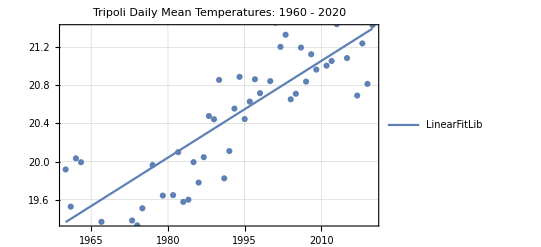

```mathematica
Show[
Plot[LinearFitLib,{x,1960,2020},PlotTheme->"Detailed"],
ListPlot[resLib2], PlotLabel->"Tripoli Daily Mean Temperatures: 1960 - 2020"]
```

#### Tripoli - Total Monthly Precipitation

Precipitation types in Tripoli are rain, with June and December 2020 receiving snow and hail, respectively. In both 2020 and 1960, Tripoli experiences months without rain.

```mathematica
WeatherData["Tripoli","PrecipitationTypes",{{2020,1},{2020,12},"Year"}]
WeatherData["Tripoli","PrecipitationTypes",{{2020,1},{2020,12},"Month"}]//Dataset
```

{{{2020,1,1},{Hail,Rain,Snow}}}

```mathematica
WeatherData["Tripoli","PrecipitationTypes",{{1960,1},{1960,12},"Year"}]
WeatherData["Tripoli","PrecipitationTypes",{{1960,1},{1960,12},"Month"}]//Dataset
```

{{{1960,1,1},{Rain}}}

We create the object for total monthly precipitation in Tripoli for the years 1960 and 2020.

```mathematica
rainData["Tripoli",2020]=WeatherData["Tripoli","TotalPrecipitation",{{2020,1},{2020,12},"Month"}];rainData["Tripoli",1960]=WeatherData["Tripoli","TotalPrecipitation",{{1960,1},{1960,12},"Month"}];
```

From both the summary statistics and the TimeShift plot of the years 1960 and 2020, it is hard to say whether 2020 is a drier year compared to 1960. In fact, excluding some peak behaviour, demonstrated by the spike in the plot and the maximum total precipitation value, which reaches 7.77 cm in December of 1960, it appears as though 2020 may be on par, if not receiving more precipitation than the year 1960. However, this may be due to one of 1960 or 2020 being exceptional years in terms of precipitation, and will be something we investigate further in the section on linear modelling.

```mathematica
summary[rainData["Tripoli", 2020]] 
summary[rainData["Tripoli", 1960]]
```

{0.,0.02,1.4025,2.91,4.62}

{0.,0.05,1.21833,0.8,7.77}

```mathematica
DateListPlot[{rainData["Tripoli",2020],TimeSeriesShift[rainData["Tripoli",1960],{60,"Year"}]},GridLines->Automatic,PlotLabels->{"2020","1960"},PlotLabel->"Monthly Total Precipitation (cm) Tripoli: 1960, 2020"]
```

-Graphics-

## 5. Linear Modelling

Expanding on the plots which we produced in the Overview Plotting section, we can produce a linear fit to plot over the data at multiple locations, in order to investigate any trends that may be present in the data. We have chosen a range of latitudes and longitudes across the gridded temperature data. In order to understand where these indexed values lie, each plot has a title representing their coordinate location, and the name of the country or region where these coordinates lie. The final section includes a graphic of all the locations we have chosen to investigate, plotted onto a world map.

### Temperature Data

Plots of temperature anomaly observations are presented for 14 global locations. The LinearModelFit is calculated based off the available data for each location, removing missing values. The linear fit along with the available data is then plotted together.

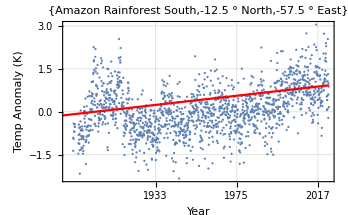

```mathematica
tempLinearFitAmazon = LinearModelFit[Select[Table[tempMeans[[i, 16, 25]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 16, 25]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks10002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Amazon Rainforest South", templat[[16]] "° North", templon[[25]] "° East"}],Plot[tempLinearFitAmazon[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

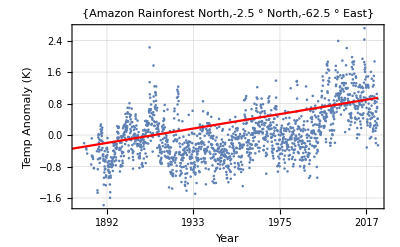

```mathematica
tempLinearFitAmazon2 = LinearModelFit[Select[Table[tempMeans[[i, 18, 24]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 18, 24]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Amazon Rainforest North", templat[[18]] "° North", templon[[24]] "° East"}],Plot[tempLinearFitAmazon2[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

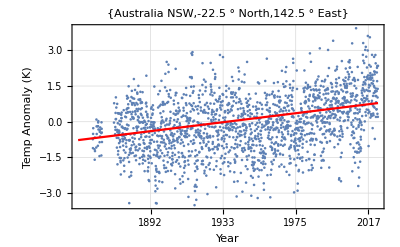

```mathematica
tempLinearFitAusNSW = LinearModelFit[Select[Table[tempMeans[[i, 14, 65]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 14, 65]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Australia NSW", templat[[14]] "° North", templon[[65]] "° East"}],Plot[tempLinearFitAusNSW[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

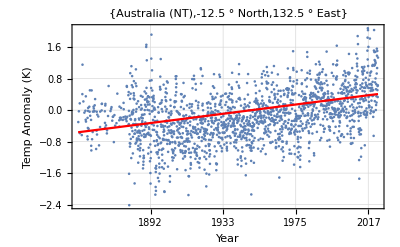

```mathematica
tempLinearFitAusNT= LinearModelFit[Select[Table[tempMeans[[i, 16, 63]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 16, 63]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Australia (NT)", templat[[16]] "° North", templon[[63]] "° East"}],Plot[tempLinearFitAusNT[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

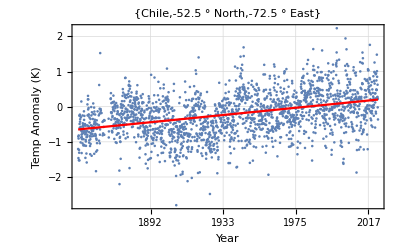

```mathematica
tempLinearFitChile = LinearModelFit[Select[Table[tempMeans[[i, 8, 22]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 8, 22]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &], FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Chile", templat[[8]] "° North", templon[[22]] "° East"}],Plot[tempLinearFitChile[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

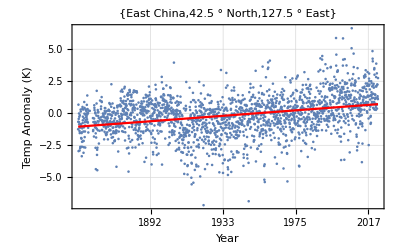

```mathematica
tempLinearFitEastChina = LinearModelFit[Select[Table[tempMeans[[i, 27, 62]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 27, 62]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &], FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"East China", templat[[27]] "° North", templon[[62]] "° East"}],Plot[tempLinearFitEastChina[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

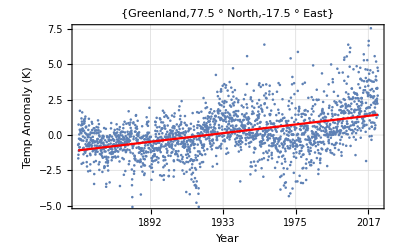

```mathematica
tempLinearFitGreenland= LinearModelFit[Select[Table[tempMeans[[i, 34, 33]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 34, 33]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Greenland", templat[[34]] "° North", templon[[33]] "° East"}],Plot[tempLinearFitGreenland[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

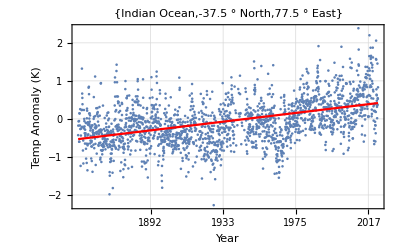

```mathematica
tempLinearFitIndianOcean = LinearModelFit[Select[Table[tempMeans[[i, 11, 52]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 11, 52]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &], FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Indian Ocean", templat[[11]] "° North", templon[[52]] "° East"}],Plot[tempLinearFitIndianOcean[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

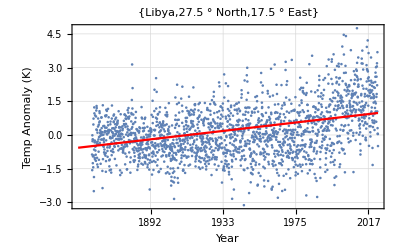

```mathematica
tempLinearFitLibya = LinearModelFit[Select[Table[tempMeans[[i, 24, 40]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 24, 40]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Libya", templat[[24]] "° North", templon[[40]] "° East"}],Plot[tempLinearFitLibya[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

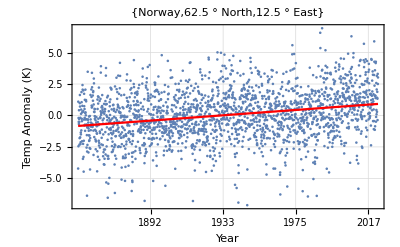

```mathematica
tempLinearFitNorway = LinearModelFit[Select[Table[tempMeans[[i, -6, 39]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, -6, 39]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Norway", templat[[-6]] "° North", templon[[39]] "° East"}],Plot[tempLinearFitNorway[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

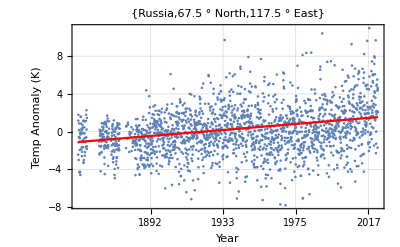

```mathematica
tempLinearFitRussia = LinearModelFit[Select[Table[tempMeans[[i, 32, 60]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 32, 60]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Russia", templat[[32]] "° North", templon[[60]] "° East"}],Plot[tempLinearFitRussia[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

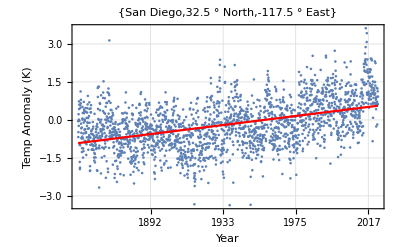

```mathematica
tempLinearFitSanDiego= LinearModelFit[Select[Table[tempMeans[[i, 25, 13]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 25, 13]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"San Diego", templat[[25]] "° North", templon[[13]] "° East"}],Plot[tempLinearFitSanDiego[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

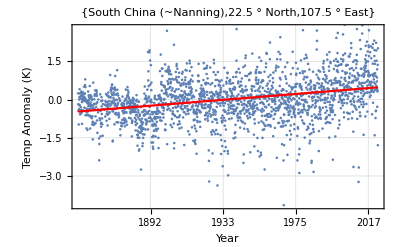

```mathematica
tempLinearFitSouthChina = LinearModelFit[Select[Table[tempMeans[[i, 23, 58]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 23, 58]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"South China (~Nanning)", templat[[23]] "° North", templon[[58]] "° East"}],Plot[tempLinearFitSouthChina[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

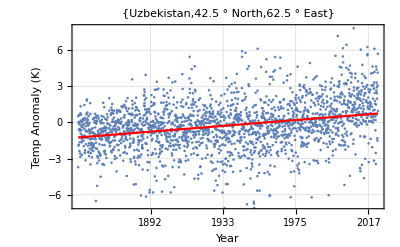

```mathematica
tempLinearFitUzbekistan = LinearModelFit[Select[Table[tempMeans[[i, 27, 49]], {i,1,Length[timeAnom]}], #≠flag &], {1,x},x];
Show[ListPlot[Select[Table[{i,tempMeans[[i, 27, 49]]}, {i, 1, Length[timeAnom]}], #[[2]]≠flag &],  FrameTicks ->{{Automatic, Automatic} ,{ticks5002000, None}}, TicksStyle->Directive[14],GridLines->Automatic,Frame->True, FrameLabel -> {{"Temp Anomaly (K)", ""}, {"Year", ""}},PlotLabel->{"Uzbekistan", templat[[27]] "° North", templon[[49]] "° East"}],Plot[tempLinearFitUzbekistan[x], {x,1,Length[timeAnom]}, PlotStyle->Red]]
```

#### Examine the Linear Fits

Let’s examine each of the linear fits to get the equation of the line, and print them along with their R-Squared value.

```mathematica
TextGrid[{{"Location","Equation", "R-Squared"},
{"Amazon South", Normal[tempLinearFitAmazon],tempLinearFitAmazon["RSquared"]},
{"Amazon North", Normal[tempLinearFitAmazon2],tempLinearFitAmazon2["RSquared"]},
{"Australia NSW", Normal[tempLinearFitAusNSW],tempLinearFitAusNSW["RSquared"]},
{"Australia NT", Normal[tempLinearFitAusNT],tempLinearFitAusNT["RSquared"]},
{"Chile", Normal[tempLinearFitChile],tempLinearFitChile["RSquared"]},
{"East China", Normal[tempLinearFitEastChina],tempLinearFitEastChina["RSquared"]},
{"Greenland", Normal[tempLinearFitGreenland],tempLinearFitGreenland["RSquared"]},
{"Indian Ocean", Normal[tempLinearFitIndianOcean],tempLinearFitIndianOcean["RSquared"]},
{"Libya", Normal[tempLinearFitLibya],tempLinearFitLibya["RSquared"]},
{"Norway", Normal[tempLinearFitNorway],tempLinearFitNorway["RSquared"]},
{"Russia", Normal[tempLinearFitRussia],tempLinearFitRussia["RSquared"]},
{"San Diego", Normal[tempLinearFitSanDiego],tempLinearFitSanDiego["RSquared"]},
{"South China", Normal[tempLinearFitSouthChina],tempLinearFitSouthChina["RSquared"]},
{"Uzbekistan", Normal[tempLinearFitUzbekistan],tempLinearFitUzbekistan["RSquared"]}},Frame ->All]
```

Location | Equation | R-Squared
Amazon South | -0.402659+0.000642207 x | 0.125683
Amazon North | -0.565979+0.000732057 x | 0.279813
Australia NSW | -0.773079+0.000752984 x | 0.114158
Australia NT | -0.562223+0.000470166 x | 0.146634
Chile | -0.648297+0.000411041 x | 0.14655
East China | -1.04678+0.000850092 x | 0.100397
Greenland | -1.08973+0.00122533 x | 0.20705
Indian Ocean | -0.531505+0.000458867 x | 0.193524
Libya | -0.568315+0.000748852 x | 0.139446
Norway | -0.833698+0.000846981 x | 0.0665708
Russia | -1.09299+0.00127411 x | 0.0777832
San Diego | -0.915427+0.000714299 x | 0.202963
South China | -0.469636+0.000460149 x | 0.094156
Uzbekistan | -1.24656+0.000963878 x | 0.0780469

We want to predict the temperature for the year 2050. In order to do this, we will estimate the number of indexes it will take to approximate this time difference. The dataset contains 2067 observations.

```mathematica
timeto2050 = UnitConvert[Quantity[timeAnom[[2067]],"Days"],"Years"][[1]]-UnitConvert[Quantity[timeAnom[[1735]],"Days"],"Years"][[1]]
1850 +UnitConvert[Quantity[timeAnom[[2067]],"Days"],"Years"][[1]] + timeto2050
```

27.6849

2050.

Subtract the index which corresponds to the correct time difference, and add it to the final index again to get the value we will substitute into the linear models.

```mathematica
(2067-1735)+2067
```

2399

The index data - point 2399 corresponds to the 1 st of January 2050. We substitute this value in for x in each of the linear models .

```mathematica
x1 = 2399
```

2399

We take the equation of the line for each location and project to 2050.

```mathematica
TextGrid[{{"Location","2050 Prediction (K)"},
{"Amazon South", tempLinearFitAmazon[x1]},
{"Amazon North", tempLinearFitAmazon2[x1]},
{"Australia NSW", tempLinearFitAusNSW[x1]},
{"Australia NT", tempLinearFitAusNT[x1]},
{"Chile", tempLinearFitChile[x1]},
{"East China", tempLinearFitEastChina[x1]},
{"Greenland", tempLinearFitGreenland[x1]},
{"Indian Ocean", tempLinearFitIndianOcean[x1]},
{"Libya", tempLinearFitLibya[x1]},
{"Norway", tempLinearFitNorway[x1]},
{"Russia", tempLinearFitRussia[x1]},
{"San Diego", tempLinearFitSanDiego[x1]},
{"South China", tempLinearFitSouthChina[x1]},
{"Uzbekistan", tempLinearFitUzbekistan[x1]}},Frame->All]
```

Location | 2050 Prediction (K)
Amazon South | 1.138
Amazon North | 1.19023
Australia NSW | 1.03333
Australia NT | 0.565705
Chile | 0.337789
East China | 0.992594
Greenland | 1.84983
Indian Ocean | 0.569317
Libya | 1.22818
Norway | 1.19821
Russia | 1.9636
San Diego | 0.798177
South China | 0.634261
Uzbekistan | 1.06578

### Precipitation Data

Recall that the Temperature Anomaly and Precipitation Anomaly datasets index latitude and longitudes using different starting points on the globe. The latitudes in the precipitation data are indexed from the Arctic [1], at 87.5^° North, to the Antarctic [36], at -87.5^° North. Longitudes are stored in degrees east from the prime meridian, with the first indexed value at 2.5^° East, returning to -2.5^° East through 72 iterations of 5^° steps Eastwards. 
This is in contrast to the temperature anomaly data, whereby latitudes are stored in reverse order, with Antarctica (-87.5^° North) stored as the 1^st index in the list, and the Arctic  (87.5^° North)  representing the 36^th index. The longitudes of the temperature data are indexed such that the first value in the list represents (-177.5^° East) through to the 72^nd index, which represents 177.5^° East. For all latitude and longitude indexing, an increase in 1 index value represents a 5^° move in the respective direction. 

In order to obtain the same latitude and longitude coordinates for both datasets, the equation to convert the indexes from the temperature dataset to the precipitation dataset is:
	PrecipLatitudeIndex = 36 - TempLatitudeIndex +1
while the conversion for the longitudes is:
	PrecipLongitudeIndex ≡ LongitudeIndex + 36  (mod 72)

Each index for the precipitation dataset is calculated as such. The linear fits are then calculated for each location for the precipitation data, and these are again plotted with the data for that location.

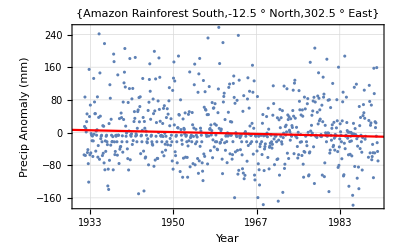

```mathematica
precipLinearFitAmazon = LinearModelFit[Select[Table[precip[[i, 21, 61]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,21, 61]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks4001100, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Amazon Rainforest South", precipLat[[21]] "° North", precipLon[[61]] "° East"}], Plot[precipLinearFitAmazon[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

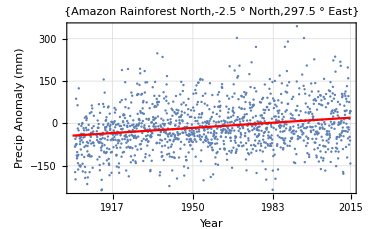

```mathematica
precipLinearFitAmazon2 = LinearModelFit[Select[Table[precip[[i, 19, 60]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,19, 60]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Amazon Rainforest North", precipLat[[19]] "° North", precipLon[[60]] "° East"}], Plot[precipLinearFitAmazon2[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

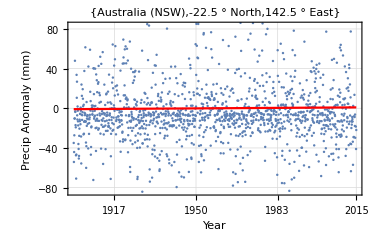

```mathematica
precipLinearFitAusNSW = LinearModelFit[Select[Table[precip[[i, 23, 29]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,23, 29]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Australia (NSW)", precipLat[[23]] "° North", precipLon[[29]] "° East"}], Plot[precipLinearFitAusNSW[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

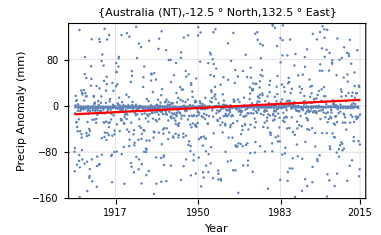

```mathematica
precipLinearFitAusNT = LinearModelFit[Select[Table[precip[[i, 21, 27]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,21, 27]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Australia (NT)", precipLat[[21]] "° North", precipLon[[27]] "° East"}], Plot[precipLinearFitAusNT[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

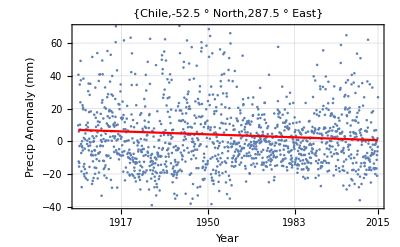

```mathematica
precipLinearFitChile = LinearModelFit[Select[Table[precip[[i, 29, 58]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,29, 58]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Chile", precipLat[[29]] "° North", precipLon[[58]] "° East"}], Plot[precipLinearFitChile[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

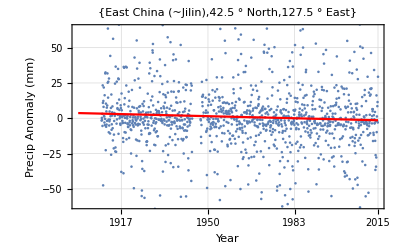

```mathematica
precipLinearFitEastChina = LinearModelFit[Select[Table[precip[[i, 10, 26]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,10,26]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"East China (~Jilin)",precipLat[[10]] "° North", precipLon[[26]] "° East"}],  Plot[precipLinearFitEastChina[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

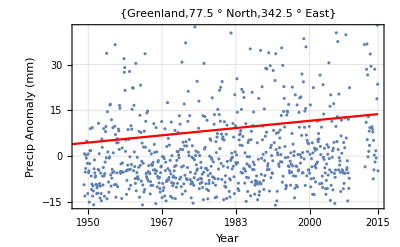

```mathematica
precipLinearFitGreenland= LinearModelFit[Select[Table[precip[[i,3, 69]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,3,69]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks6001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Greenland", precipLat[[3]] "° North", precipLon[[69]] "° East"}], Plot[precipLinearFitGreenland[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

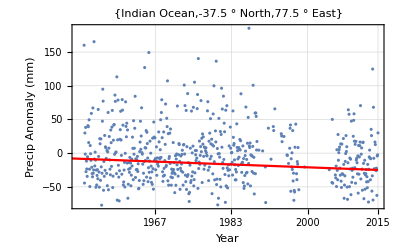

```mathematica
precipLinearFitIndianOcean= LinearModelFit[Select[Table[precip[[i, 26, 16]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,26,16]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks8001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Indian Ocean", precipLat[[26]] "° North", precipLon[[16]] "° East"}], Plot[precipLinearFitIndianOcean[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

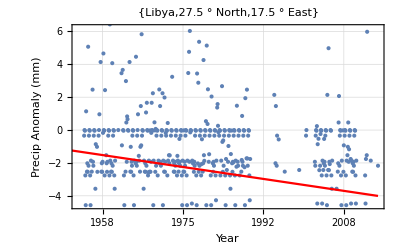

```mathematica
precipLinearFitLibya = LinearModelFit[Select[Table[precip[[i, 13, 4]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,13,4]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks7001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Libya", precipLat[[13]] "° North", precipLon[[4]] "° East"}], 
Plot[precipLinearFitLibya[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

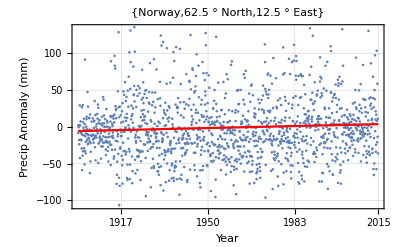

```mathematica
precipLinearFitNorway = LinearModelFit[Select[Table[precip[[i, 6, 3]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,6, 3]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Norway", precipLat[[6]] "° North", precipLon[[3]] "° East"}],  Plot[precipLinearFitNorway[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

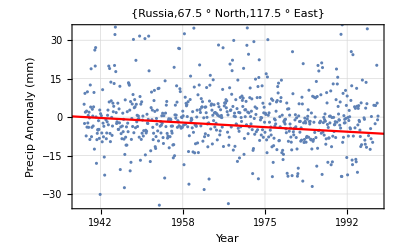

```mathematica
precipLinearFitRussia = LinearModelFit[Select[Table[precip[[i, 5, 24]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,5, 24]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks5001100, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Russia", precipLat[[5]] "° North", precipLon[[24]] "° East"}], Plot[precipLinearFitRussia[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

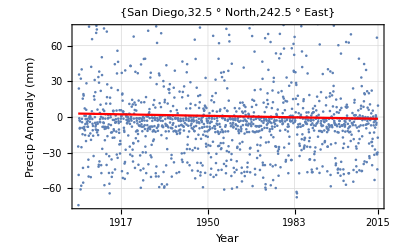

```mathematica
precipLinearFitSanDiego = LinearModelFit[Select[Table[precip[[i, 12, 49]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,12, 49]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"San Diego", precipLat[[12]] "° North", precipLon[[49]] "° East"}], Plot[precipLinearFitSanDiego[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

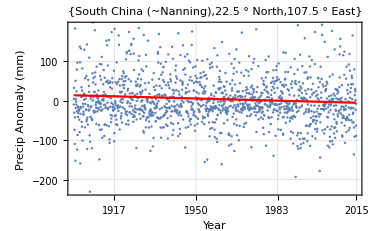

```mathematica
precipLinearFitSouthChina = LinearModelFit[Select[Table[precip[[i, 14, 22]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,14, 22]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"South China (~Nanning)", precipLat[[14]] "° North", precipLon[[22]] "° East"}], Plot[precipLinearFitSouthChina[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

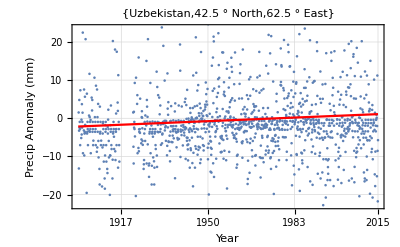

```mathematica
precipLinearFitUzbekistan = LinearModelFit[Select[Table[precip[[i, 10, 13]], {i,1,Length[precipTime]}], #≠precipFlag &], {1,x},x];
Show[ListPlot[Select[Table[{i,precip[[i,10,13]]},{i,1,Length[precipTime]}],#[[2]]≠precipFlag&],  Frame->True , FrameTicks ->{{Automatic, Automatic} ,{pticks2001400, None}},TicksStyle->Directive[14],GridLines->Automatic,Frame->True,FrameLabel -> {{"Precip Anomaly (mm)", ""}, {"Year", ""}},PlotLabel->{"Uzbekistan",precipLat[[10]] "° North", precipLon[[13]] "° East"}], Plot[precipLinearFitUzbekistan[x], {x,1,Length[precipTime]}, PlotStyle->Red]]
```

#### Examine the linear fits

Extract the linear fits of each of the locations investigated along with their R-Squared values

```mathematica
TextGrid[{{"Location","Equation", "R-Squared"},
{"Amazon South", Normal[precipLinearFitAmazon],precipLinearFitAmazon["RSquared"] },
{"Amazon North", Normal[precipLinearFitAmazon2],precipLinearFitAmazon2["RSquared"]},
{"Australia NSW", Normal[precipLinearFitAusNSW],precipLinearFitAusNSW["RSquared"]},
{"Australia NT", Normal[precipLinearFitAusNT],precipLinearFitAusNT["RSquared"]},
{"Chile", Normal[precipLinearFitChile],precipLinearFitChile["RSquared"]},
{"East China", Normal[precipLinearFitEastChina],precipLinearFitEastChina["RSquared"]},
{"Greenland", Normal[precipLinearFitGreenland],precipLinearFitGreenland["RSquared"]},
{"Indian Ocean", Normal[precipLinearFitIndianOcean],precipLinearFitIndianOcean["RSquared"]},
{"Libya", Normal[precipLinearFitLibya],precipLinearFitLibya["RSquared"]},
{"Norway", Normal[precipLinearFitNorway],precipLinearFitNorway["RSquared"]},
{"Russia", Normal[precipLinearFitRussia],precipLinearFitRussia["RSquared"]},
{"San Diego", Normal[precipLinearFitSanDiego],precipLinearFitSanDiego["RSquared"]},
{"South China", Normal[precipLinearFitSouthChina],precipLinearFitSouthChina["RSquared"]},
{"Uzbekistan", Normal[precipLinearFitUzbekistan],precipLinearFitUzbekistan["RSquared"]}},Frame->All]
```

Location | Equation | R-Squared
Amazon South | 14.4598-0.0223568 x | 0.00387557
Amazon North | -43.167+0.0459319 x | 0.0493158
Australia NSW | -0.886423+0.0012918 x | 0.000174569
Australia NT | -14.4744+0.0179651 x | 0.0103401
Chile | 6.91114-0.00451547 x | 0.00664121
East China | 3.67702-0.00368541 x | 0.00215195
Greenland | -2.68772+0.0118797 x | 0.0391291
Indian Ocean | 4.45104-0.0212133 x | 0.00832001
Libya | 1.01763-0.00362809 x | 0.00954079
Norway | -5.65038+0.00682159 x | 0.00401628
Russia | 4.12693-0.00893086 x | 0.0161761
San Diego | 2.91079-0.00316456 x | 0.00115514
South China | 14.1752-0.0137683 x | 0.00696255
Uzbekistan | -2.15986+0.00234216 x | 0.00793126

We have to again approximate the correct indexing difference between the start of the observations and the year 2050. There are 1385 observations in the precipitation dataset.

```mathematica
preciptimeto2050 = UnitConvert[Quantity[precipTime[[1385]],"Days"],"Years"][[1]]-UnitConvert[Quantity[precipTime[[971]],"Days"],"Years"][[1]]
1800 +UnitConvert[Quantity[precipTime[[1385]],"Days"],"Years"][[1]] + preciptimeto2050
```

34.5178

2049.99

The difference between the

```mathematica
(1385-971)+1385
```

1799

We take the equation of the line for each location and project to 2050.

```mathematica
x2 = 1799 (* Index point which corresponds to 2050 *)
```

1799

```mathematica
TextGrid[{{"Location","2050 Prediction (mm)"},
{"Amazon South", precipLinearFitAmazon[x2]},
{"Amazon North",precipLinearFitAmazon2[x2]},
{"Australia NSW",precipLinearFitAusNSW[x2]},
{"Australia NT",precipLinearFitAusNT[x2]},
{"Chile",precipLinearFitChile[x2]},
{"East China",precipLinearFitEastChina[x2]},
{"Greenland",precipLinearFitGreenland[x2]},
{"Indian Ocean",precipLinearFitIndianOcean[x2]},
{"Libya",precipLinearFitLibya[x2]},
{"Norway",precipLinearFitNorway[x2]},
{"Russia",precipLinearFitRussia[x2]},
{"San Diego",precipLinearFitSanDiego[x2]},
{"South China",precipLinearFitSouthChina[x2]},
{"Uzbekistan",precipLinearFitUzbekistan[x2]}},Frame->All]
```

Location | 2050 Prediction (mm)
Amazon South | -25.7601
Amazon North | 39.4644
Australia NSW | 1.43753
Australia NT | 17.8448
Chile | -1.21219
East China | -2.95303
Greenland | 18.6838
Indian Ocean | -33.7116
Libya | -5.50931
Norway | 6.62167
Russia | -11.9397
San Diego | -2.78226
South China | -10.5939
Uzbekistan | 2.05369

### Gridded Locations

Accessing each of the indexed locations which we chose to investigate above, we have a plot of the globe to visualise these coordinate locations. The “With” expression allows us to specify each location, with the function plotting each of these locations one at a time. The dimensions of the “precipLat” and “precipLon” lists are 36 and 72 respectively, so we can change these indexes accordingly, to plot a new location.

```mathematica
With[{locations={GeoPosition[{precipLat[[10]],precipLon[[26]]}],
GeoPosition[{precipLat[[10]],precipLon[[13]]}],GeoPosition[{precipLat[[3]],precipLon[[69]]}],
GeoPosition[{precipLat[[6]],precipLon[[3]]}], 
GeoPosition[{precipLat[[5]],precipLon[[24]]}], GeoPosition[{precipLat[[13]],precipLon[[4]]}],GeoPosition[{precipLat[[26]],precipLon[[16]]}],
GeoPosition[{precipLat[[29]],precipLon[[58]]}], GeoPosition[{precipLat[[19]],precipLon[[60]]}],GeoPosition[{precipLat[[21]],precipLon[[61]]}],
GeoPosition[{precipLat[[21]],precipLon[[27]]}],GeoPosition[{precipLat[[23]],precipLon[[29]]}],
GeoPosition[{precipLat[[12]],precipLon[[49]]}],
GeoPosition[{precipLat[[14]],precipLon[[22]]}]}},GeoGraphics[{GeoStyling["ReliefMap"],Red,GeoMarker[locations]},GeoRange->"World", ImageSize->Large, PlotLabel->Style["World Map", 16]]]
```

-Graphics-

## 6. Carbon Dioxide

There are three CO_2data-sets which we will discuss here. They are the data-sets on global trend in CO_2between 2012 and 2022, global annual estimates since 1959 and global monthly estimates since 1958. The data-sets are made freely available by the NOAA Global Monitoring Laboratory. All CO_2 data presented here is given in parts per million (ppm).

### CO_2 Global Trend 2012 - 2022

Estimates in the daily global CO_2 are taken from four baseline observatories of the GML in:

Barrow, Alaska

Mauna Loa, Hawaii

American Samoa

The South Pole, Antarctica

The global seasonal cycle in CO_2 is estimated from averaging CO_2 data at each of the observatories. A smoothed, deseasonalised variable is presented along with a trend variable across time for daily date points from the 1st of January 2012 to the most recently available time-point upon download - the 25th of July 2022.

#### Estimated CO2 Daily Global Seasonal Cycle and Trend (ppm) over the last ten years (2012 - 2022).

The global trend in CO2 over the last ten years are displayed below. There are 3859 observations in the data-sets across variables year, month, day, smoothed and trend. A moving average has been applied to the trend data in order to estimated the deseasonalised cycle.

```mathematica
globalTrend[[2;;, ;;]]//Dimensions
globalTrend[[;;6,;;]]//Dataset
```

{3859,5}

```mathematica
globalTrend[[3860, ;;]]//Dataset (* latest time-point in the data-set *)
```

Create the variables for smoothed and trend data from the data-set.

```mathematica
smoothed = globalTrend[[2;;,4]]; (* All rows, 4th column *)
trend = globalTrend[[2;;,5]];
```

Similar to previous sections, we apply the summary object to data variables to provide an indication of summary statistics. We plot too a box-plot of the trend data in order to get an idea of the spread of data across all time-points.

{391.48,397.85,404.686,411.44,417.48}

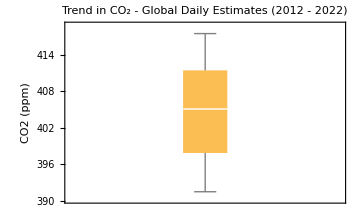

```mathematica
summary[trend]
BoxWhiskerChart[trend, ImageSize->Medium,PlotLabel->"Trend in CO_2 - Global Daily Estimates (2012 - 2022)", FrameLabel->{"","CO2 (ppm)"}]
```

For the dates between 2012 to 2022 there is a spread between 390 ppm and 420 ppm in the CO_2 trend data. Mean trend value is 404.686 ppm.

-Graphics-

There is a trend upward across time with seasonal fluctuations repeated year on year and sustained at peak levels across many days.

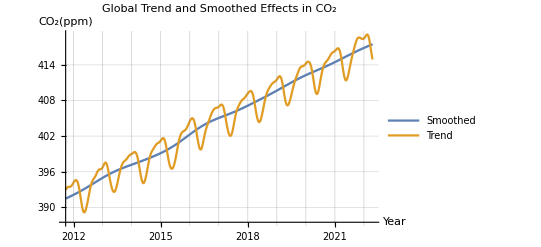

```mathematica
ListLinePlot[{trend, smoothed},  PlotLegends->{"Smoothed", "Trend" }, PlotLabel->"Global Trend and Smoothed Effects in CO_2",  AxesLabel->{"Year", "CO_2(ppm)"}, Ticks->{tickListCO1, Automatic}, GridLines->Automatic]
```

### Annual Mean CO_2 1959 - 2021

Annual mean CO_2 at Mauna Loa Observatory is compiled by the GML. Within the meta-data it is noted that data between March 1958, when the data starts, and April 1974 is collected by geochemist C. David Keeling, in association with the Scripps Institution of Oceanography (SIO).

The data contains 63 observations across the variables year, mean global annual CO_2 and uncertainty. The most recent year included in the data-set is for 2021. The standard deviation of the differences of annual mean values in CO_2is used to quantify uncertainty. However, uncertainty values across all time points are 0.12 ppm.

#### Annual mean CO_2at Mauna Loa, Hawaii 1958 - 2021

```mathematica
annualCO2[[2;;,;;]]//Dimensions
annualCO2[[;;6, ;;]]//Dataset
```

{63,3}

We create the mean object in order to extract summary statistics and create a box-plot. The average global CO_2 value between 1958 to 2021 is 357.338 ppm, which is approximately 50 ppm lower than the average value for daily estimates from 2012 to 2022.
The box-plot shows a spread in CO_2estimates in the range 320ppm to 420 ppm.

```mathematica
mean = annualCO2[[2;;, 2]];(* all rows, 2nd column *)
```

{315.98,330.19,357.338,382.09,416.45}

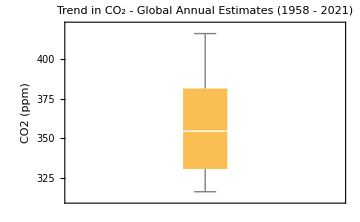

```mathematica
summary[mean]
BoxWhiskerChart[mean, ImageSize->Medium,PlotLabel->"Trend in CO_2 - Global Annual Estimates (1958 - 2021)", FrameLabel->{"","CO2 (ppm)"}]
```

The trend line is a relatively smooth curve upward over time, and does not display the seasonality of the data. This indicates that the seasonality occurs within the year, rather than across larger time intervals.

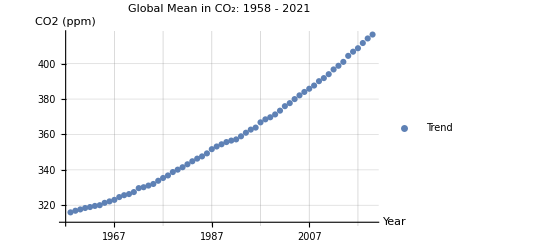

```mathematica
ListPlot[{mean},  PlotLegends->{"Trend", "Smoothed" }, PlotLabel->"Global Mean in CO_2: 1958 - 2021",  AxesLabel->{"Year", "CO2 (ppm)"}, Ticks->{tickListCO2, Automatic}, GridLines->Automatic]
```

### Monthly CO2 Data from Mauna Loa 1958 - 2022

Global monthly CO_2 estimates are also taken at Mauna Loa Observatory in Hawaii. Reference to C. David Keeling at SIO is again given in the meta-data, applying for the data March 1958 to April 1974.

The data contains 772 observations across the variables year, month, decimal data, average  CO_2 , deseasonalised CO_2,number of days, standard deviation and uncertainty. The monthly estimates are constructed from daily mean values, and the ndays variables indicates the number of days available from each month. Missing data in the data-set is given in the forms:

ndays: -1

sdev: -9.99

unc: -0.99

These variables do not form a core part of our analysis, but will be analysed further in a final subsection.

#### Monthly Global CO_2Estimates at Mauna Loa, Hawaii 1958 - 2022.

Monthly data from Mauna Loa. We look at the monthly data in order to better see the seasonality effects in the data.

```mathematica
monthlyCO2[[2;;,;;]]//Dimensions
monthlyCO2[[;;6,;;]]//Dataset
```

{772,8}

We can delineate the columns in the dataset by assigning named variables.

```mathematica
year =  monthlyCO2[[2;;,1]];
average = monthlyCO2[[2;;,4]];
deseasonalised = monthlyCO2[[2;;,5]];
sdev = monthlyCO2[[2;;,7]];
unc = monthlyCO2[[2;;,8]];
```

We see the box-whisker plot and summary statistics are very similar to the annual CO_2 data from the same time period. Mean average CO_2 is 357.278 ppm.

{312.43,329.56,357.278,382.02,420.99}

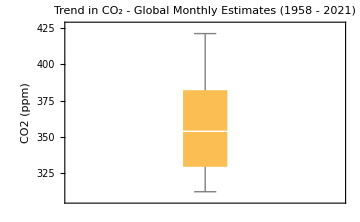

```mathematica
summary[average]
BoxWhiskerChart[average, ImageSize->Medium,PlotLabel->"Trend in CO_2 - Global Monthly Estimates (1958 - 2021)", FrameLabel->{"","CO2 (ppm)"}]
```

#### Seasonality within the monthly data

From plotting the average CO2 data, we see there is clearly a trend upwards across time. Evident too is the fact that there is seasonality within the data. We can overlay the de-seasonalised data in order to see clearly the moving average.  Look up seasonality in CO2 in google Scholar.

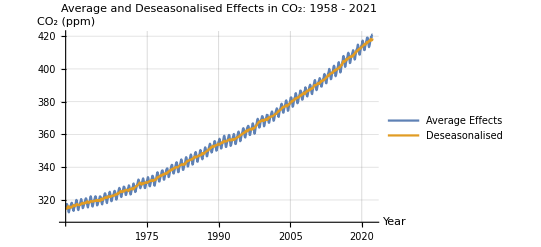

```mathematica
ListLinePlot[{average, deseasonalised},  PlotLegends->{"Average Effects", "Deseasonalised" }, PlotLabel->"Average and Deseasonalised Effects in CO_2: 1958 - 2021", Ticks->{tickListCO3, Automatic}, AxesLabel->{"Year", "CO_2 (ppm)"}, GridLines->Automatic]
```

#### Plot seasonality across the year

In order to take a closer inspection of seasonality occurring in the monthly CO_2 data we look at a group of four dates , separated by 20 years:

1959, 1960, 1961

1979, 1980, 1981

1999, 2000, 2001

2019, 2020, 2021

We carry out some initial data set-up in order to extract the dates of interest.

```mathematica
Range[1959, 2019, 20]
```

{1959,1979,1999,2019}

1959, 1960, 1961.

```mathematica
monthlyCO2[[12;;23, ;;]]//Dataset;(* 1959 only *)
monthlyCO2[[24;;35, ;;]]//Dataset;
monthlyCO2[[36;;47, ;;]]//Dataset;
average[[12;;23]]; (*1959 *)
average[[24;;35]];(*1960 *)
average[[36;;47]]; (*1961 *)
```

1979, 1980, 1981.

```mathematica
monthlyCO2[[252;;263,;;]]//Dataset;
monthlyCO2[[264;;275,;;]]//Dataset;
monthlyCO2[[276;;287,;;]]//Dataset;
average[[252;;263]] ;(*1979 *)
average[[264;;275]] ;(*1980 *)
average[[276;;287]]; (*1981 *)
```

1999, 2000, 2001.

```mathematica
monthlyCO2[[492;;503,;;]]//Dataset;
monthlyCO2[[504;;515,;;]]//Dataset;
monthlyCO2[[516;;527,;;]]//Dataset;
average[[492;;503]] ;(*1999 *)
average[[504;;515]] ;(*2000 *)
average[[516;;527]]; (*2001 *)
```

2019, 2020, 2021.

```mathematica
monthlyCO2[[732;;743,;;]]//Dataset;
monthlyCO2[[744;;755,;;]]//Dataset;
monthlyCO2[[756;;767,;;]]//Dataset;
average[[732;;743]] ;(*2019 *)
average[[744;;755]] ;(*2020 *)
average[[756;;767]] ;(*2021 *)
```

We plot the four groups of years. Year on year across the plots, we see that seasonality reaches peak values approximately a third of the way through the year in April. CO_2 levels decrease there-after, and reach pit values at approximately the 8th and 9th months of the year, before increasing again. The literature review showed that seasonality within CO_2 was caused predominantly by the effects of photosynthesis, with a focus on the effects of forests in the Northern Hemisphere, where CO_2 seasonality has been shown to display larger swings in seasonality compared against Southern Hemisphere or latitudes close to the equator.

```mathematica
ListPlot[{average[[36;;47]] , average[[24;;35]] ,average[[12;;23]]},  PlotLabels-> {"1961", "1960" , "1959"},PlotLabel->Style["Annual Average Effects CO_2 (ppm)", 16], AxesLabel->{"Month","CO2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[276;;287]], average[[264;;275]] ,average[[252;;263]] },  PlotLabels-> {"1981", "1980" , "1979"}, PlotLabel->Style["Annual Average Effects CO_2 (ppm)", 16],AxesLabel->{"Month","CO_2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[516;;527]] , average[[504;;515]] ,average[[492;;503]]},PlotLabels-> {"2001", "2000" , "1999"},   PlotLabel->Style["Annual Average Effects CO_2 (ppm)", 16],AxesLabel->{"Month","CO_2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
ListPlot[{average[[756;;767]], average[[744;;755]] ,average[[732;;743]] },PlotLabels-> {"2021", "2020" , "2019"},  PlotLabel->Style["Annual Average Effects CO_2 (ppm)", 16],AxesLabel->{"Month","CO_2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Comparing  1960 and 2020, we see the seasonal effects of both years are diminished by the effects of the respective year. The CO_2 levels for 2020 are 100 ppm higher than CO_2 levels for 1960.

```mathematica
ListPlot[{  average[[744;;755]], average[[24;;35]]  },PlotLabels-> {"2020" , "1960"},  PlotLabel->Style["Annual Average Effects CO2", 16],AxesLabel->{"Month","CO_2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

Despite not appearing so, CO2 data from 2020 still forms strong peaks and troughs, which is muted out somewhat when compared against different time periods.

```mathematica
ListPlot[{  average[[744;;755]]},PlotLabels-> {"2020" , "1960"},  PlotLabel->Style["Annual Average Effects CO2", 16],AxesLabel->{"Month","CO_2 (ppm)"}, Ticks->{Range[1,12,1], Automatic}]
```

-Graphics-

#### Standard Deviation

There are 196 missing data points in standard deviation, which have been replaced by -9.99. We choose to replace these values instead with 0.

```mathematica
Count[sdev, -9.99]
```

196

```mathematica
sdev2 = ReplaceAll[sdev, -9.99 -> 0];
```

We can construct the 95% confidence interval for the data as the average ± 1.96 ((standard deviation)/(√(sample size))).

```mathematica
z = 1.96;
n = 772; (* sample size *)
sdev//Dimensions;
```

```mathematica
UB95 = average + z* (sdev/(√n));
LB95 = average - z* (sdev/(√n));
```

We plot the 95% confidence bounds and average. It is hard to discriminate the three data-lines due to low uncertainty values.

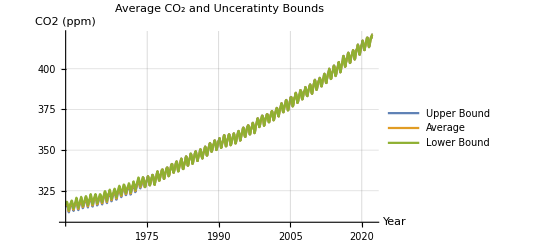

```mathematica
ListLinePlot[{UB95,average,  LB95},AxesLabel->{"Year", "CO2 (ppm)"},Ticks->{tickListCO3, Automatic},   PlotLegends->{"Upper Bound", "Average" , "Lower Bound"}, GridLines->Automatic, PlotLabel->"Average CO_2 and Unceratinty Bounds"]
```

Let’s look at 2010 to 2020 only.

```mathematica
UB10 = UB95[[624;;755]];
LB10 = LB95[[624;;755]];
avg10 = average[[624;;755]];
```

```mathematica
tickList4 = {{24, "2012"}, {48, "2014"}, {72, "2016"}, {96, "2018"}, {120, "2020"}};
```

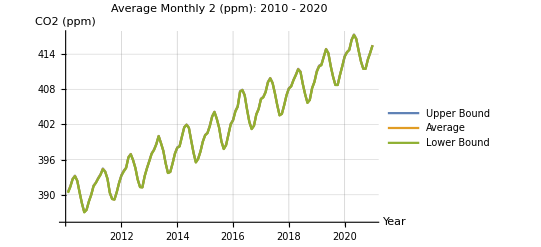

```mathematica
ListLinePlot[{UB10,avg10,  LB10}, AxesLabel->{"Year", "CO2 (ppm)"},   PlotLabel->"Average Monthly 2 (ppm): 2010 - 2020",  PlotLegends->{"Upper Bound", "Average" , "Lower Bound"}, Ticks->{tickList4, Automatic}, GridLines->Automatic]
```

Overall, the confidence bounds appear to line up very closely with the average curve, indicating that the uncertainty in estimates is low.